```mathematica
SetDirectory["/Users/micciche/CORSI/CORSO_INTRO-COMPL_2022-2023/EROGATO_2023-2024/LEZIONI/LEZIONE_24/CODICI"]
```

/Users/micciche/CORSI/CORSO_INTRO-COMPL_2022-2023/EROGATO_2023-2024/LEZIONI/LEZIONE_24/CODICI

```mathematica
iter=1000;
NN=10^5;
```

## Example 1 - Gaussian

### from population

```mathematica
(*popolazione*)
mu=3;
sigma=0.4;
sigmasq=sigma^2;
```

```mathematica
(*genero iter random samples dalla distribuzione della popolazione*)
Do[data[st]=RandomVariate[NormalDistribution[mu,sigma],NN],
    {st,1,iter}]
```

```mathematica
(*calcolo la media del random sample*)
Do[M[st]=Mean[data[st]],
    {st,1,iter}]
```

3.00005

0.00123194

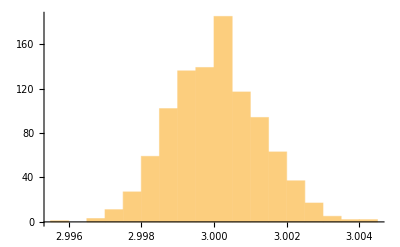

```mathematica
(*distribuzione della media del random sample*)
tabM=Table[M[st],{st,1,iter}];
emme=Mean[tabM]
esse=StandardDeviation[tabM]
essesq=esse^2;
Histogram[tabM]
```

```mathematica
{mu,emme}
{sigma/Sqrt[NN],esse}
```

{3,3.00005}

{0.00126491,0.00123194}

### from bootstrap

```mathematica
EMP=RandomVariate[NormalDistribution[mu,sigma],NN];
muEMP=Mean[EMP]
sigmaEMP=StandardDeviation[EMP]
{mu,muEMP}
{sigma,sigmaEMP}
```

3.00134

0.399937

{3,3.00134}

{0.4,0.399937}

```mathematica
Do[index[st]=Table[RandomInteger[{1,NN}],{n,1,NN}],
    {st,1,iter}]
(*genero iter random samples dalla distribuzione delle copie di bootstrap*)
Do[datab[st]=Table[EMP[[index[st][[n]]]],{n,1,NN}],
    {st,1,iter}]
```

```mathematica
Table[{st,Length[datab[st]],Length[datab[st]//Union]},{st,1,10}]//TableForm
```

1 | 100000 | 63171
2 | 100000 | 63128
3 | 100000 | 63133
4 | 100000 | 63149
5 | 100000 | 63277
6 | 100000 | 63179
7 | 100000 | 63182
8 | 100000 | 63207
9 | 100000 | 63211
10 | 100000 | 63150

```mathematica
(*calcolo la media delle copie di bootstrap*)
Do[Mb[st]=Mean[datab[st]],
    {st,1,iter}]
```

3.00132

0.00125237

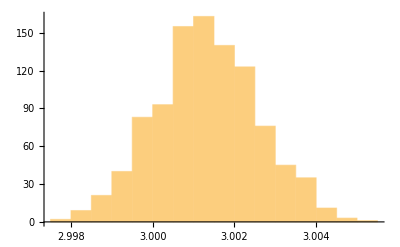

```mathematica
(*distribuzione della media delle copie di bootstrap*)
tabMb=Table[Mb[st],{st,1,iter}];
emmeb=Mean[tabMb]
esseb=StandardDeviation[tabMb]
essesqb=esseb^2;
Histogram[tabMb]
```

```mathematica
{mu,muEMP,emmeb}
{sigma/Sqrt[NN],sigmaEMP/Sqrt[NN],esseb}
```

{3,3.00134,3.00132}

{0.00126491,0.00126471,0.00125237}

## Example 2 - Student T

### from population

```mathematica
(*popolazione*)
mu=3;
scale=0.4;
ngdl=5;
Mean[StudentTDistribution[mu,scale,ngdl]]
sigma=StandardDeviation[StudentTDistribution[mu,scale,ngdl]]
sigmasq=sigma^2;
```

3

0.516398

```mathematica
(*genero iter random samples dalla distribuzione della popolazione*)
Do[data[st]=RandomVariate[StudentTDistribution[mu,scale,ngdl],NN],
    {st,1,iter}]
```

```mathematica
(*calcolo la media del random sample*)
Do[M[st]=Mean[data[st]],
    {st,1,iter}]
```

3.00013

0.00163675

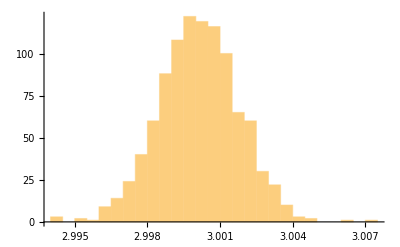

```mathematica
(*distribuzione della media del random sample*)
tabM=Table[M[st],{st,1,iter}];
emme=Mean[tabM]
esse=StandardDeviation[tabM]
essesq=esse^2;
Histogram[tabM]
```

```mathematica
{mu,emme}
{sigma/Sqrt[NN],esse}
```

{3,3.00013}

{0.00163299,0.00163675}

### from bootstrap

```mathematica
EMP=RandomVariate[StudentTDistribution[mu,scale,ngdl],NN];
muEMP=Mean[EMP]
sigmaEMP=StandardDeviation[EMP]
{mu,muEMP}
{sigma,sigmaEMP}
```

3.00027

0.516624

{3,3.00027}

{0.516398,0.516624}

```mathematica
Do[index[st]=Table[RandomInteger[{1,NN}],{n,1,NN}],
    {st,1,iter}]
(*genero iter random samples dalla distribuzione delle copie di bootstrap*)
Do[datab[st]=Table[EMP[[index[st][[n]]]],{n,1,NN}],
    {st,1,iter}]
```

```mathematica
Table[{st,Length[datab[st]],Length[datab[st]//Union]},{st,1,10}]//TableForm
```

1 | 100000 | 63003
2 | 100000 | 63184
3 | 100000 | 63246
4 | 100000 | 63169
5 | 100000 | 63227
6 | 100000 | 63280
7 | 100000 | 63267
8 | 100000 | 63349
9 | 100000 | 63267
10 | 100000 | 63273

```mathematica
(*calcolo la media delle copie di bootstrap*)
Do[Mb[st]=Mean[datab[st]],
    {st,1,iter}]
```

3.0003

0.00165825

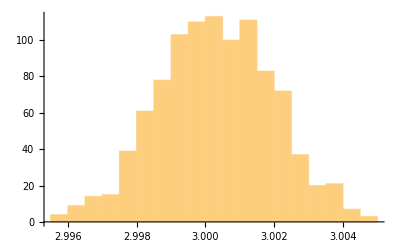

```mathematica
(*distribuzione della media delle copie di bootstrap*)
tabMb=Table[Mb[st],{st,1,iter}];
emmeb=Mean[tabMb]
esseb=StandardDeviation[tabMb]
essesqb=esseb^2;
Histogram[tabMb]
```

```mathematica
{mu,muEMP,emmeb}
{sigma/Sqrt[NN],sigmaEMP/Sqrt[NN],esseb}
```

{3,3.00027,3.0003}

{0.00163299,0.00163371,0.00165825}